## Set the constants and formulas

```mathematica
Slpg=24;
PV=50;
Day=45;
Month=23Day;
```

```mathematica
PL[POut_,PIn_]:=(POut-PIn)PV-Slpg;
```

## Import the data and select the interval of interest

```mathematica
SetDirectory[NotebookDirectory[]];
Data=Import["SY-5min.asc","FieldSeparators"->","];
Length[Data]
```

357433

```mathematica
nStart=100000;
nStop=100050;
Do[If[Data[[i,2]]=="09:35",{nStartDay=i;Break[];}],{i,nStart,nStop}]
```

```mathematica
nStartDay
```

100037

```mathematica
Data[[nStartDay]]
```

{01/08/91,09:35,440.5,442.,440.,441.75,0}

## HH and LL precomputation

```mathematica
ChLengthMax=10000;
ChLengthMin=500;
ChJump=100;
NKids=Quotient[ChLengthMax-ChLengthMin,ChJump]
TradeStart=nStartDay;
TradeStop=TradeStart+12Month+ChLengthMax-1
DataOHLC=Table[{Data[[i,3]],Data[[i,4]],Data[[i,5]],Data[[i,6]]},{i,TradeStart,TradeStop+ChLengthMax,1}];
Length[DataOHLC]
```

95

122456

32420

```mathematica
HighList=Table[DataOHLC[[i,2]],{i,1,Length[DataOHLC]}];
LowList=Table[DataOHLC[[i,3]],{i,1,Length[DataOHLC]}];
StartChannelHigh=Table[DataOHLC[[i,2]],{i,1,ChLengthMax}];
StartChannelLow=Table[DataOHLC[[i,3]],{i,1,ChLengthMax}];
OrderListHigh=Ordering[StartChannelHigh];
OrderListLow=Ordering[StartChannelLow];
Do[
HHArrayKids[ChLengthMax+1,j]=Max[StartChannelHigh];
StartChannelHigh=Drop[StartChannelHigh,ChJump];
LLArrayKids[ChLengthMax+1,j]=Min[StartChannelLow];
StartChannelLow=Drop[StartChannelLow,ChJump];
,{j,0,NKids,1}];
{Dynamic[i],ProgressIndicator[Dynamic[i],{ChLengthMax+1,TradeStop-TradeStart+1}]}
```

{,}

```mathematica
Do[
OrderListHigh=DeleteCases[OrderListHigh,i-ChLengthMax];
OrderListLow=DeleteCases[OrderListLow,i-ChLengthMax];
Do[If[HighList[[i]]≤HighList[[OrderListHigh[[j]]]],{OrderListHigh=Insert[OrderListHigh,i,j];Break[];}],{j,1,ChLengthMax-1}];
Do[If[LowList[[i]]≤LowList[[OrderListLow[[j]]]],{OrderListLow=Insert[OrderListLow,i,j];Break[];}],{j,1,ChLengthMax-1}];
If[Length[OrderListHigh]==ChLengthMax-1,OrderListHigh=Append[OrderListHigh,i];];
If[Length[OrderListLow]==ChLengthMax-1,OrderListLow=Append[OrderListLow,i];];
HHArrayKids[i+1,0]=HighList[[OrderListHigh[[ChLengthMax]]]];
LLArrayKids[i+1,0]=LowList[[OrderListLow[[1]]]];
Do[
Do[If[OrderListHigh[[k]]>i-ChLengthMax+j*ChJump,{
HHArrayKids[i+1,j]=HighList[[OrderListHigh[[k]]]];Break[];}],{k,ChLengthMax,1,-1}];
Do[If[OrderListLow[[k]]>i-ChLengthMax+j*ChJump,{
LLArrayKids[i+1,j]=LowList[[OrderListLow[[k]]]];Break[];}],{k,1,ChLengthMax,1}];
,{j,1,NKids}]
,{i,ChLengthMax+1,TradeStop-TradeStart+1,1}]
```

### Export

```mathematica
Export["HH95KidsYear1.dat",Table[HHArrayKids[i,j],{i,ChLengthMax+1,TradeStop-TradeStart+1,1},{j,0,NKids}]]
Export["LL95KidsYear1.dat",Table[LLArrayKids[i,j],{i,ChLengthMax+1,TradeStop-TradeStart+1,1},{j,0,NKids}]]
```

HH95KidsYear1.dat

LL95KidsYear1.dat

### Check

```mathematica
MasterCheckList={};
Do[
HHCheckList={};LLCheckList={};
Do[
HHCheckList=Append[HHCheckList,Max[Table[DataOHLC[[k,2]],{k,i-(ChLengthMax-ChJump*j),i-1,1}]]];
LLCheckList=Append[LLCheckList,Min[Table[DataOHLC[[k,3]],{k,i-(ChLengthMax-ChJump*j),i-1,1}]]];
,{i,ChLengthMax+1,TradeStop-TradeStart+1,1}];
HHArrayToList=Table[HHArrayKids[i,j],{i,ChLengthMax+1,TradeStop-TradeStart+1,1}];
LLArrayToList=Table[LLArrayKids[i,j],{i,ChLengthMax+1,TradeStop-TradeStart+1,1}];
MasterCheckList=Append[MasterCheckList,
{Max[HHCheckList-HHArrayToList],Min[HHCheckList-HHArrayToList],Max[LLCheckList-LLArrayToList],Min[LLCheckList-LLArrayToList]}];
,{j,0,NKids}]
MasterCheckList
```

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

## The main code

### Main loop

```mathematica
MPTemp=0;MP=0;Equity=0;TargetPrice=0;HH=0;LL=0;EntryPrice=0;PrevPeak=0;PrevTrough=0;DD=0;
EquityList=Table[{i,0},{i,1,ChLength}];
MPList=EquityList;HHList=EquityList;LLList=EquityList;EPList=EquityList;TPList=EquityList;DDList=EquityList;
EquityMax=0;MaxDD=0;
Timing[Do[
CurrentOpen=DataOHLC[[i,1]];
CurrentHigh=DataOHLC[[i,2]];
CurrentLow=DataOHLC[[i,3]];
PreviousClose=DataOHLC[[i-1,4]];
If[Equity>EquityMax,EquityMax=Equity;];
DD=Equity-EquityMax;
If[DD<MaxDD,MaxDD=DD;];
If[MP==0,{
HH=Max[Table[DataOHLC[[j,2]],{j,i-ChLength,i-1,1}]];
LL=Min[Table[DataOHLC[[j,3]],{j,i-ChLength,i-1,1}]];
If[CurrentHigh>HH&&CurrentOpen<HH,{MPTemp=+1;EntryPrice=HH;}];
If[CurrentHigh>HH&&CurrentOpen≥HH,{MPTemp=+1;EntryPrice=CurrentOpen;}];
If[CurrentLow<LL&&CurrentOpen>LL,{MPTemp=-1;EntryPrice=LL;}];
If[CurrentLow<LL&&CurrentOpen≤LL,{MPTemp=-1;EntryPrice=CurrentOpen;}];
}];
If[MP==+1,{
PrevPeak=EntryPrice;
If[PreviousClose>PrevPeak,PrevPeak=PreviousClose;];
TargetPriceRaw=PrevPeak(1-StpPct);
TargetPrice=(Quotient[TargetPriceRaw,0.25]+Quotient[Mod[TargetPriceRaw,0.25],0.125])*0.25;
If[TargetPrice>CurrentLow&&TargetPrice<CurrentHigh,{Equity=Equity+PL[TargetPrice,EntryPrice];MPTemp=0;}];
}];
If[MP==-1,{
PrevTrough=EntryPrice;
If[PreviousClose<PrevTrough,PrevTrough=PreviousClose;];
TargetPriceRaw=PrevTrough(1+StpPct);
TargetPrice=(Quotient[TargetPriceRaw,0.25]+Quotient[Mod[TargetPriceRaw,0.25],0.125])*0.25;
If[TargetPrice>CurrentLow&&TargetPrice<CurrentHigh,{Equity=Equity+PL[EntryPrice,TargetPrice];MPTemp=0;}];
}];
MP=MPTemp;
,{i,ChLength+1,TradeStop-TradeStart+1,1}];]
Equity/Abs[MaxDD]
```

{323.858,Null}

3.6483

### Plot the equity and drawdown curves

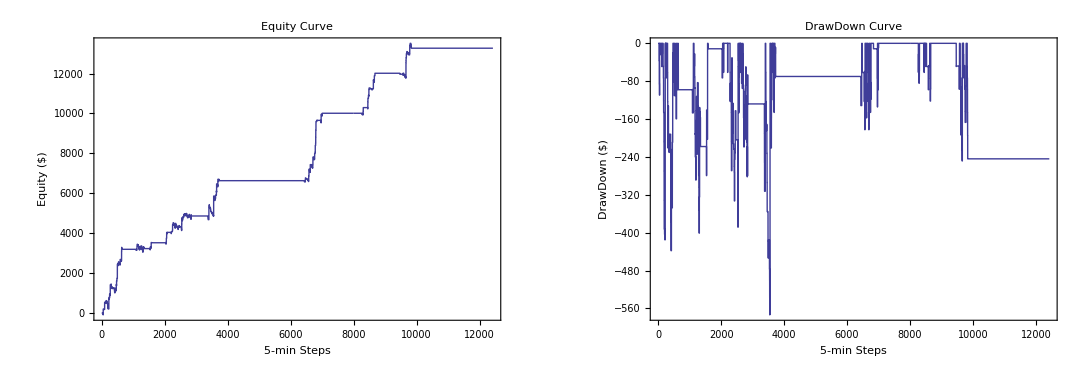

```mathematica
GraphicsGrid[{{
ListPlot[EquityList,Joined->True,AxesOrigin->{0,0},ImageSize->500,PlotRange->All,Frame->True,AspectRatio->0.7,FrameLabel->{Style["5-min Steps",FontSize->12,Italic,Bold],Style["Equity ($)",FontSize->12,Italic,Bold]},LabelStyle->{Directive[Black,10],FontFamily->"Calibri"},RotateLabel->True,PlotLabel->Style["Equity Curve",FontSize->15,Italic,Bold]],
ListPlot[DDList,Joined->True,AxesOrigin->{0,0},ImageSize->500,PlotRange->All,Frame->True,AspectRatio->0.7,FrameLabel->{Style["5-min Steps",FontSize->12,Italic,Bold],Style["DrawDown ($)",FontSize->12,Italic,Bold]},LabelStyle->{Directive[Black,10],FontFamily->"Calibri"},RotateLabel->True,PlotLabel->Style["DrawDown Curve",FontSize->15,Italic,Bold]]
}}]
```

### Optimization parameter: ratio of the final net equity over the maximum drawdown

```mathematica
RoA=Equity/Abs[Min[DDList]]
```

23.1343